# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\Chaotic_eigenfunctions

```mathematica
(*Operators*)
Clear[Sz,SM,Sm,Sx,Sy,F];
Sz[J_]:=DiagonalMatrix[Table[-J+k-1,{k,1,2J+1}]];
SM[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i+1)],{i,-J,J-1}],1];
Sm[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i-1)],{i,-J+1,J}],-1];
Sx[J_]:=(1/2)(SM[J]+Sm[J]);
Sy[J_]:=Sy[J]=(1/(2I))(SM[J]-Sm[J]);
Clear[Floq];
Floq[J_,α_,k_,τ_]:=N[MatrixExp[(-I*k/(2J))(Sx[J].Sx[J])].MatrixExp[(-I*α*τ)(Sz[J])]];
Clear[a2];
a2[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J,J}],20]]
];
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

# Method

```mathematica
radius=1.99999;
delta=0.03;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
boundaryPoints=Select[gridPoints,Abs[Norm[#]^2-radius^2]<=2-1.99999&];
circlePoints=Select[gridPoints,Norm[#]<radius&];
region=Join[boundaryPoints,circlePoints];
region//Length
```

13952

```mathematica
ListPlot[region,AspectRatio->1];
```

```mathematica
Clear[J];
J=100;
α=0.84;
τ=1;
```

```mathematica
rotation=MatrixExp[I(N[Pi])Sx[J]];
rotation2=MatrixExp[I(N[α/2])Sz[J]];
rotation3=MatrixExp[I(N[-α/2])Sz[J]];
```

```mathematica
cohes=ParallelTable[Quiet[a2[J,i[[1]],i[[2]]]],{i,region}];
```

```mathematica
Clear[husimi];
husimi[ψ_]:=ParallelTable[{region[[i,1]],region[[i,2]],Abs[Conjugate[cohes[[i]]].ψ]^2},{i,Length[region]}]
```

```mathematica
k=2.5;
(*mat=ConjugateTranspose[rotation2].Floq[J,α,k,τ].rotation2;*)
mat=ConjugateTranspose[rotation3].ConjugateTranspose[rotation].Floq[J,α,k,τ].rotation.rotation3;
matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
eigenvalM=Eigenvalues[matM];
eigenvalm=Eigenvalues[matm];
matm=Table[mat[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
eigenvecM=Eigenvectors[matM];
eigenvecm=Eigenvectors[matm];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
```

```mathematica
data=husimi[neweigenvec[[2]]];
```

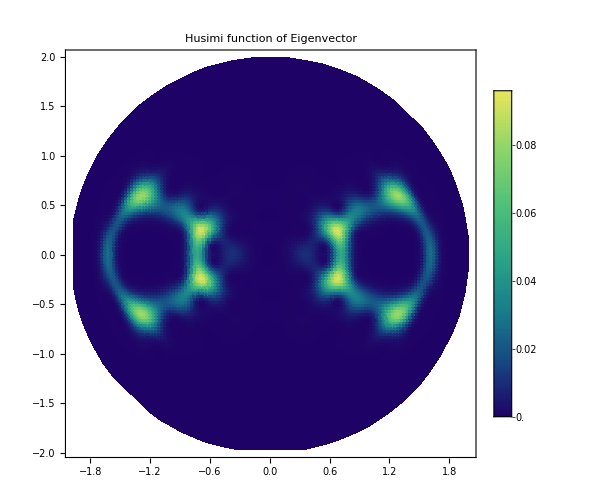

```mathematica
ListDensityPlot[data,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",ImageSize->500,PlotLabel->Style["Husimi function of Eigenvector",25,Black]]
```

```mathematica
d2=ParallelTable[Total[Abs[Conjugate[neweigenvec].i]^4],{i,cohes}];
```

```mathematica
newd2=Transpose[{region[[All,1]],region[[All,2]],-Log[d2]/Log[2J+1]}];
```

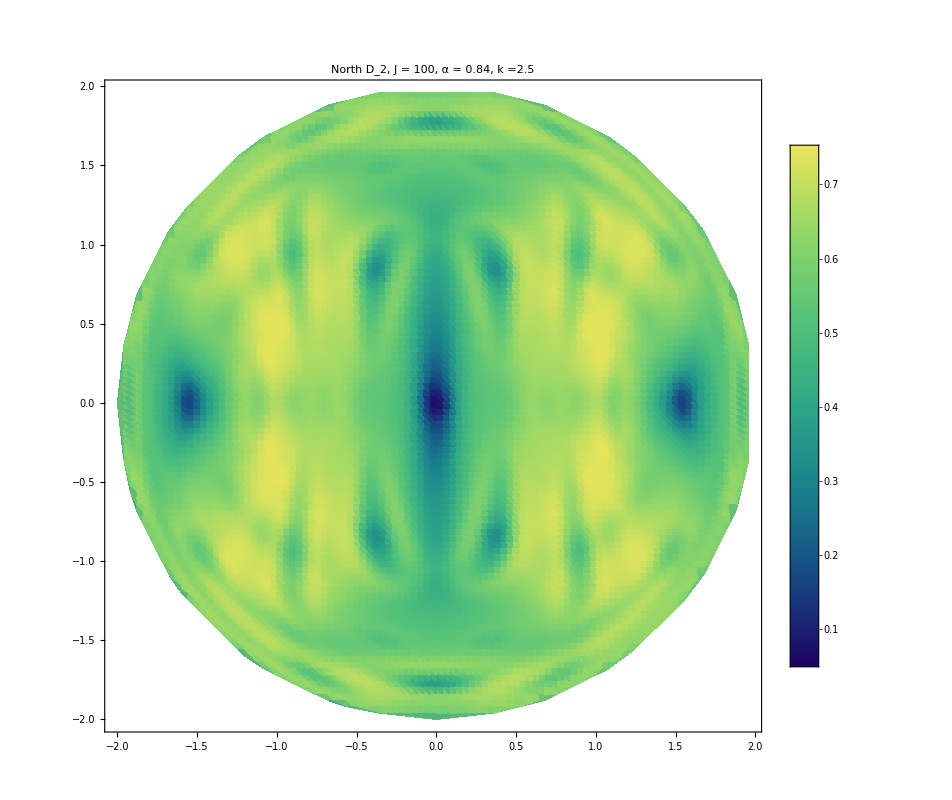

```mathematica
d2plotn=ListDensityPlot[newd2,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["North D_2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k],25,Black],ImageSize->800]
```

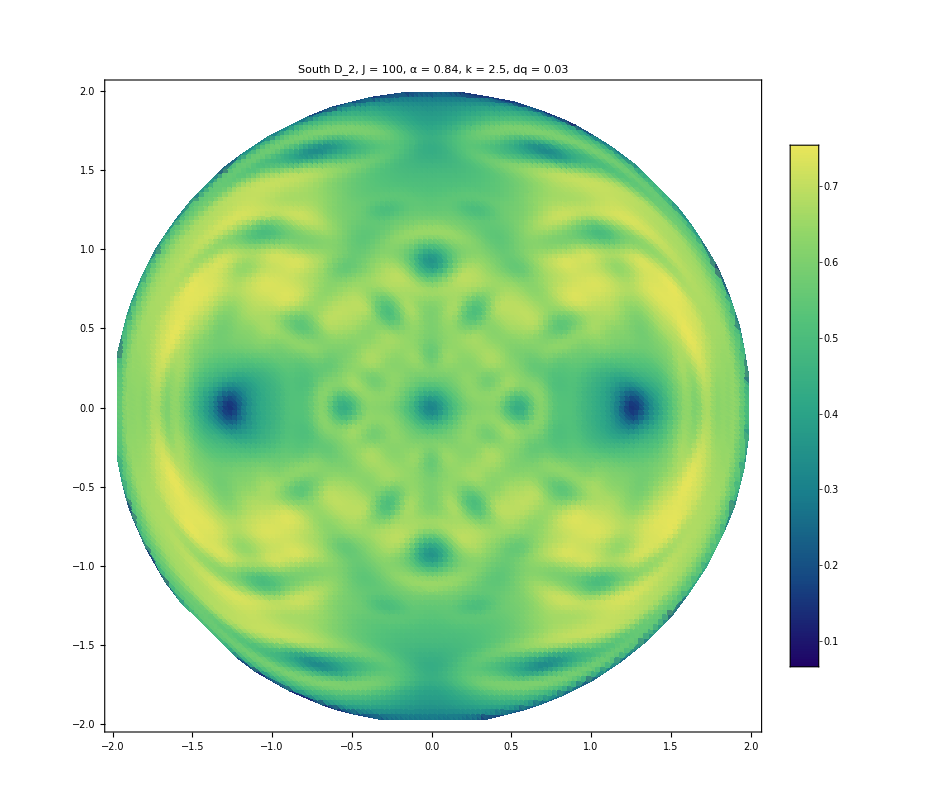

```mathematica
d2plots=ListDensityPlot[newd2,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["South D_2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta],25,Black],ImageSize->800]
```

```mathematica
Export["d2north_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>".png",d2plotn]
```

d2north_J_100_alpha_0.84_k_2.5.png

```mathematica
Export["d2south_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[delta]<>".png",d2plots]
```

d2south_J_100_alpha_0.84_k_2.5_dq_0.03.png

```mathematica
allhusimis=Table[husimi[i],{i,neweigenvec}];
newhusimis=Table[Transpose[{i[[All,1]],i[[All,2]],i[[All,3]]/Total[i[[All,3]]]}],{i,allhusimis}];
iprs=Table[Total[Abs[i[[All,3]]]^2],{i,newhusimis}];
```

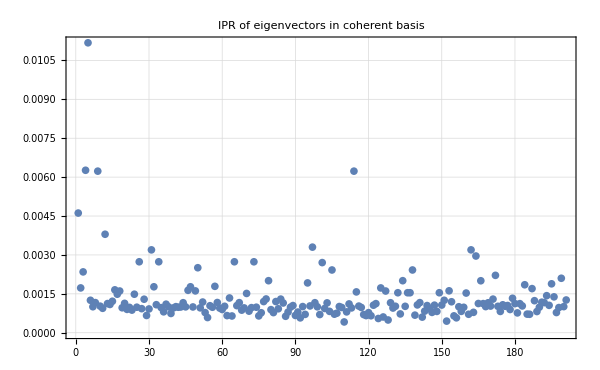

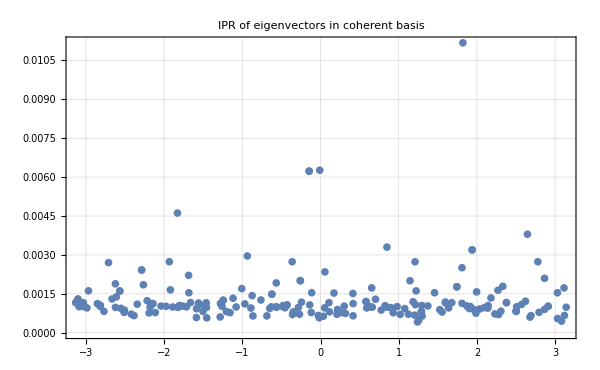

```mathematica
ListPlot[iprs,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["IPR of eigenvectors in coherent basis",25,Black],ImageSize->600]
ListPlot[Transpose[{Arg[neweigenval],iprs}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["IPR of eigenvectors in coherent basis",25,Black],ImageSize->600]
```

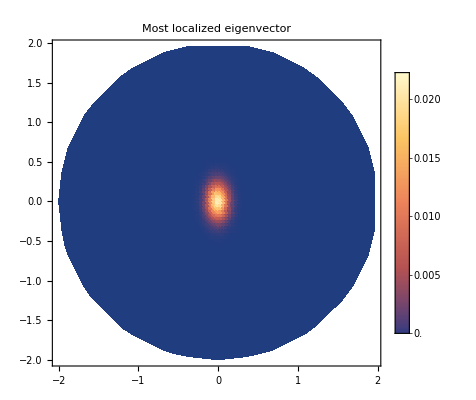

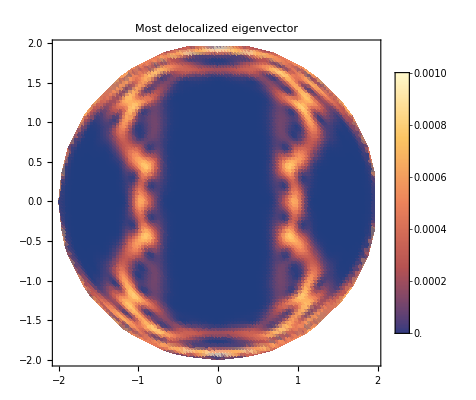

```mathematica
ListDensityPlot[newhusimis[[5]],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["Most localized eigenvector",25,Black]]
ListDensityPlot[newhusimis[[152]],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["Most delocalized eigenvector",25,Black]]
```

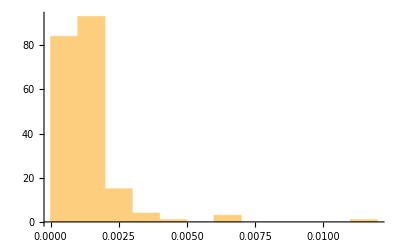

```mathematica
Histogram[iprs,15]
```

```mathematica
allhusimisb=Table[husimi[i],{i,neweigenvec}];
newhusimisb=Table[Transpose[{i[[All,1]],i[[All,2]],i[[All,3]]/Total[i[[All,3]]]}],{i,allhusimisb}];
iprsb=Table[Total[Abs[i[[All,3]]]^2],{i,newhusimisb}];
```

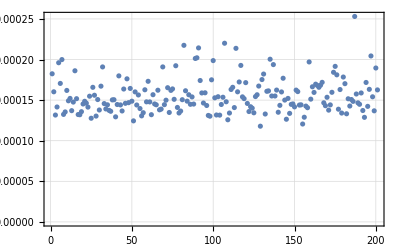

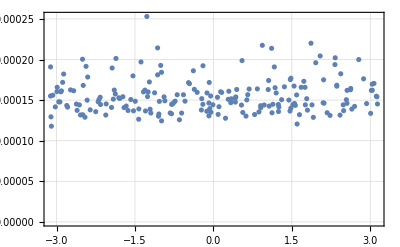

```mathematica
ListPlot[iprsb,PlotRange->All,PlotTheme->"Detailed"]
ListPlot[Transpose[{Arg[neweigenval],iprsb}],PlotRange->All,PlotTheme->"Detailed"]
```

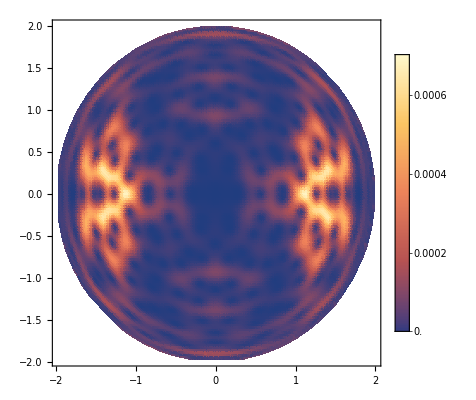

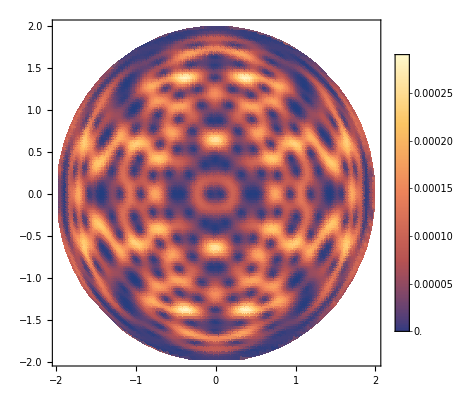

```mathematica
ListDensityPlot[newhusimisb[[187]],PlotRange->All,PlotTheme->"Detailed"]
ListDensityPlot[newhusimisb[[129]],PlotRange->All,PlotTheme->"Detailed"]
```

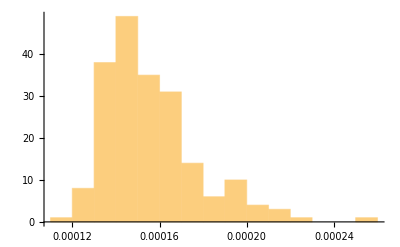

```mathematica
Histogram[iprsb,15]
```

```mathematica
allhusimisc=Table[husimi[i],{i,neweigenvec}];
newhusimisc=Table[Transpose[{i[[All,1]],i[[All,2]],i[[All,3]]/Total[i[[All,3]]]}],{i,allhusimisc}];
iprsc=Table[Total[Abs[i[[All,3]]]^2],{i,newhusimisc}];
```

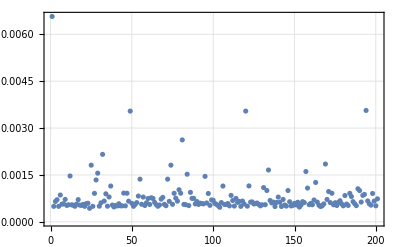

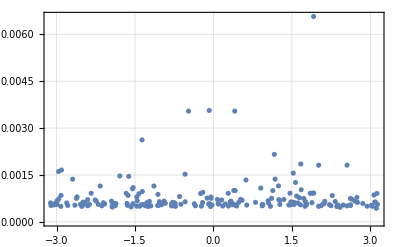

```mathematica
ListPlot[iprsc,PlotRange->All,PlotTheme->"Detailed"]
ListPlot[Transpose[{Arg[neweigenval],iprsc}],PlotRange->All,PlotTheme->"Detailed"]
```

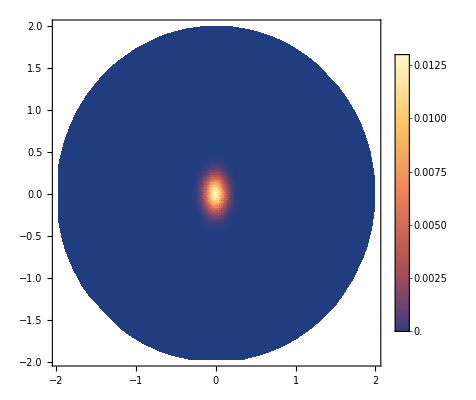

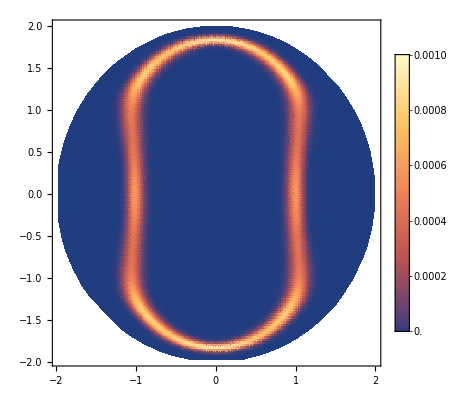

```mathematica
ListDensityPlot[newhusimisc[[1]],PlotRange->All,PlotTheme->"Detailed"]
ListDensityPlot[newhusimisc[[117]],PlotRange->All,PlotTheme->"Detailed"]
```

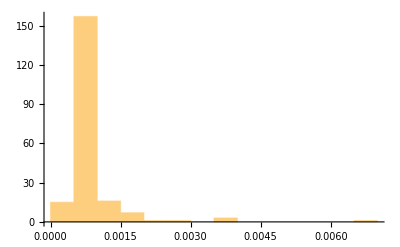

```mathematica
Histogram[iprsc,15]
```

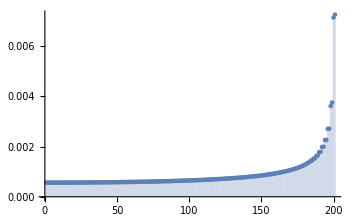

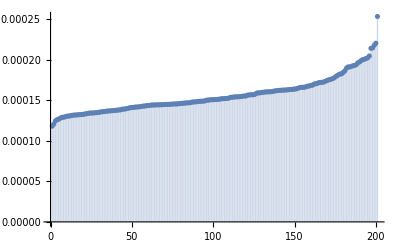

```mathematica
ListPlot[Sort[iprs],PlotRange->All,Filling->Axis]
ListPlot[Sort[iprsb],PlotRange->All,Filling->Axis]
```

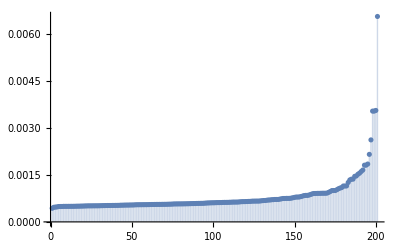

```mathematica
ListPlot[Sort[iprsc],PlotRange->All,Filling->Axis]
```

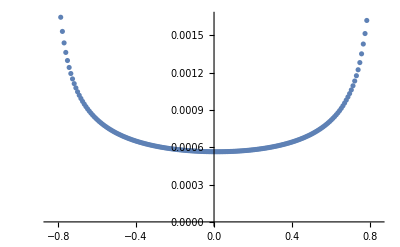

```mathematica
ope=(α/J)Sz[J];
jzs=ParallelTable[Chop[Conjugate[i].ope.i],{i,neweigenvec}];
ListPlot[Transpose[{jzs,iprs}]]
```

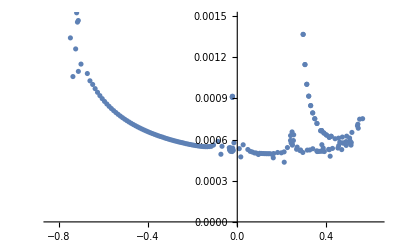

```mathematica
ope=(α/J)Sz[J];
jzs=ParallelTable[Chop[Conjugate[i].ope.i],{i,neweigenvec}];
ListPlot[Transpose[{jzs,iprsc}]]
```

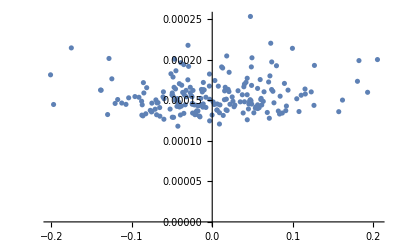

```mathematica
ope=(α/J)Sz[J];
jzs=ParallelTable[Chop[Conjugate[i].ope.i],{i,neweigenvec}];
ListPlot[Transpose[{jzs,iprsb}]]
```